## V0 interface

```mathematica
SetDirectory[NotebookDirectory[]];
<<nf.wl;
vFiles = FileNames["*.txt"]
```

{C1 d150_v.txt,C1 d300_v.txt,C1 d600_v.txt,C1 d900_v.txt,C2 d150_v.txt,C2 d300_v.txt,C2 d600_v.txt,C2 d900_v.txt,C3 d150_v.txt,C3 d300_v.txt,C3 d600_v.txt,C3 d900_v.txt}

#### Make grids of all samples If you turn off Auto, it is recommended to only check off one plot at a time In the contours box, you can insert a single integer or a list of numbers

```mathematica
interfaceSelectors
```

|  |  |  |  |  |  |  |  |  |  | 
 |  |  | 
Reduce range to 0.1 C/m^2 	 Eliminate zeros 	 Plot contour 	 Plot 3D 	 Labels 	 Export 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
Auto

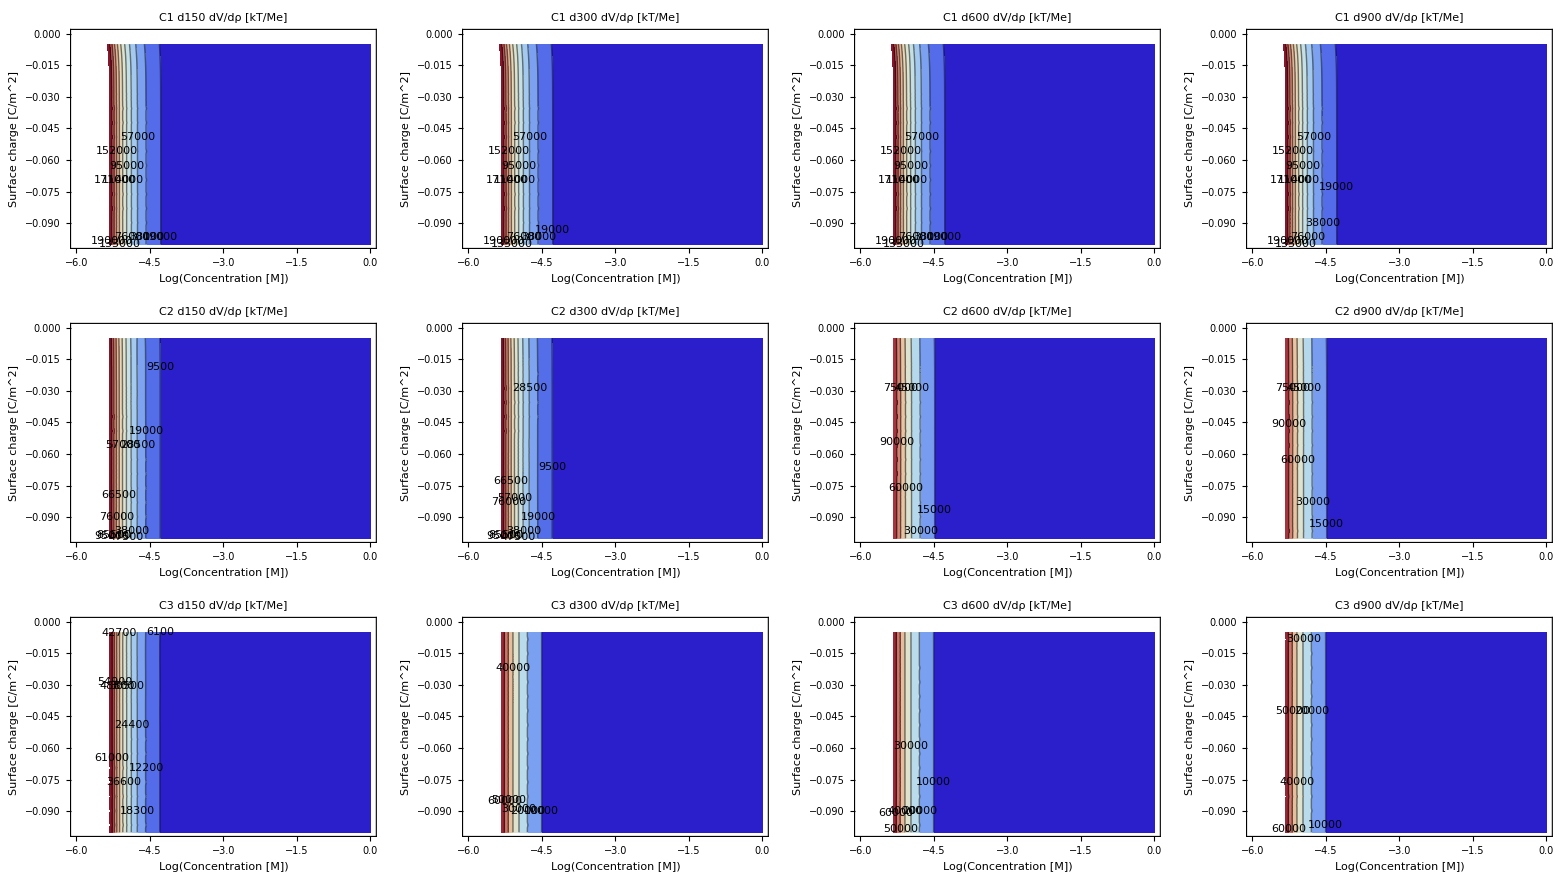
Log(dV/dρ) [kT/Me]
-Graphics-

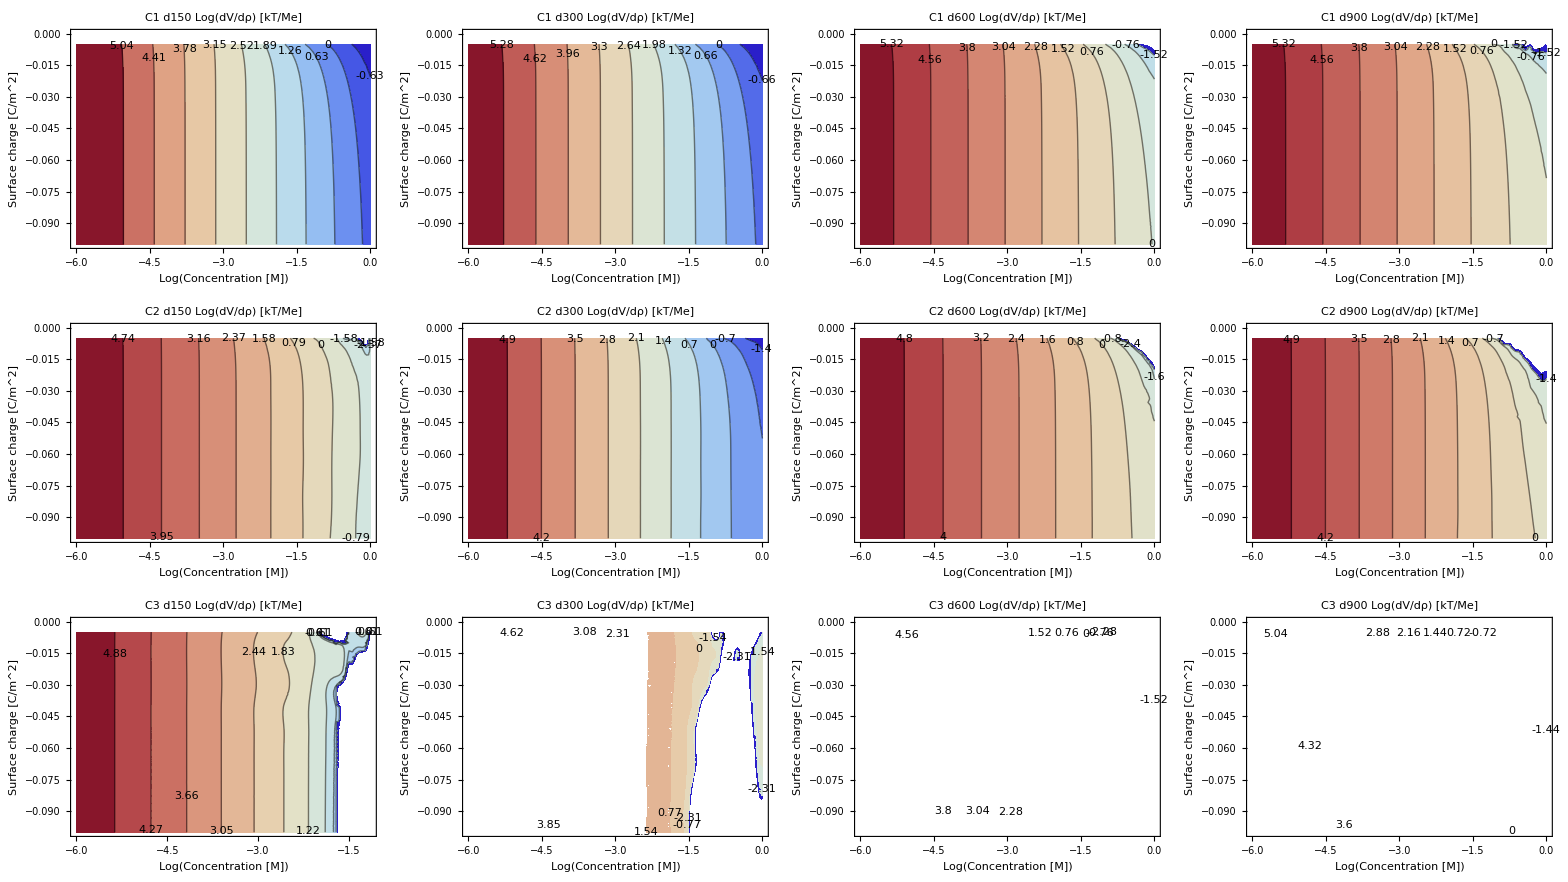
dV/dρ [kT/Me]
-Graphics-

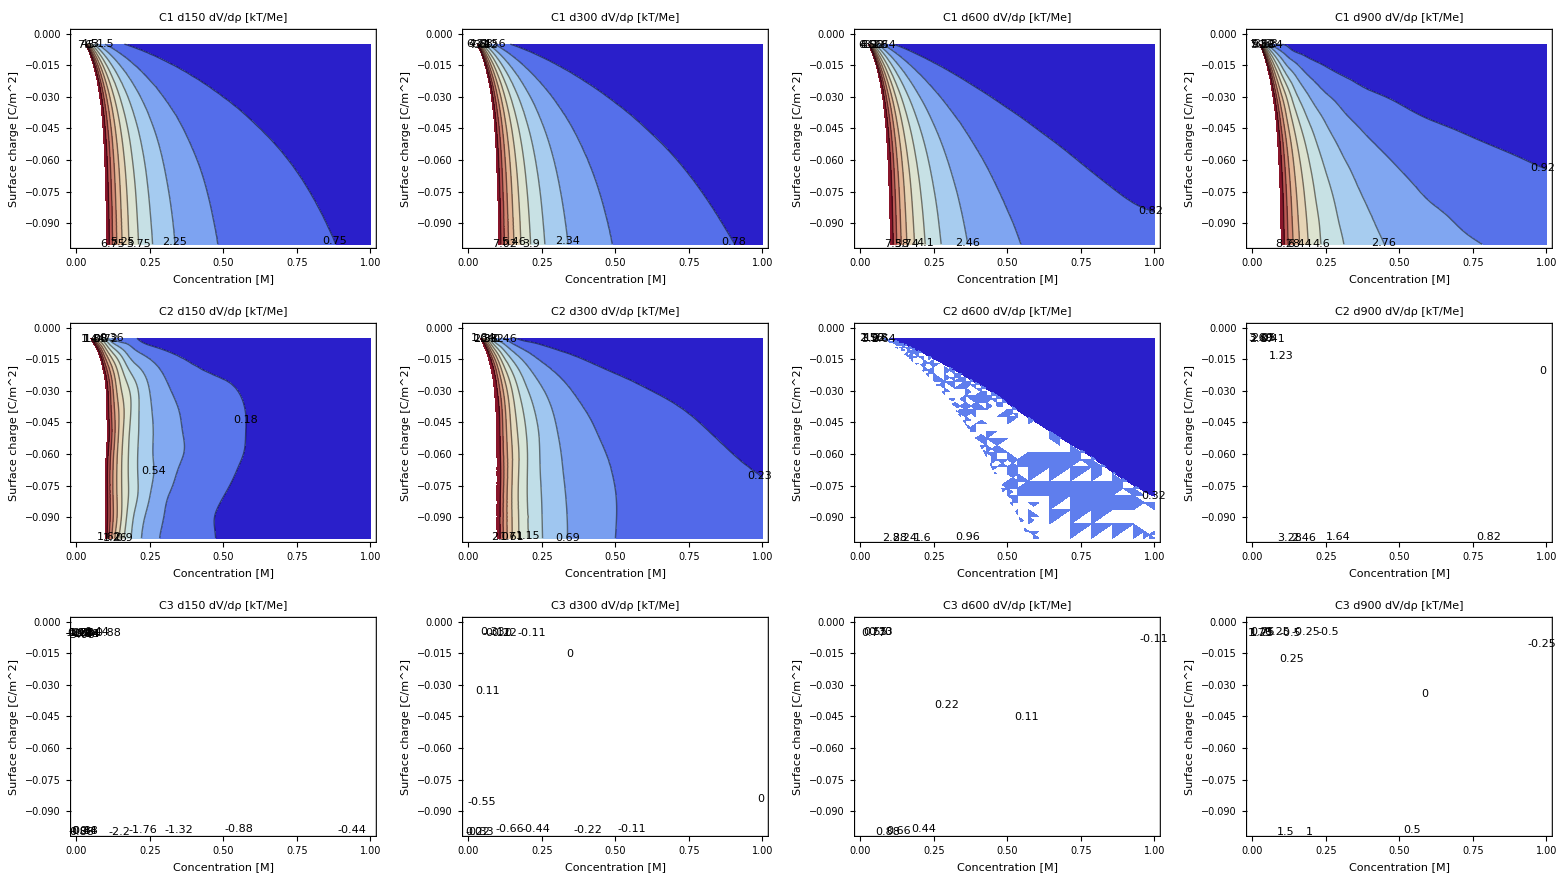
dV/dρ [kT/Me]
-Graphics-

```mathematica
makeGrids[redRange, noZeros, vFiles,flist, contour,d3, {ToExpression[minZ], ToExpression[maxZ]}, contours, cf,labels, export, autoRange]
```

#### Make plots for single samples Recommended - check Auto

```mathematica
interfaceSelectors
```

|  |  |  |  |  |  |  |  |  |  | 
 |  |  | 
Reduce range to 0.1 C/m^2 	 Eliminate zeros 	 Plot contour 	 Plot 3D 	 Labels 	 Export 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
Auto

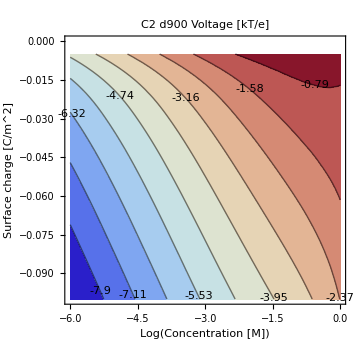

```mathematica
Row[graphMaker[redRange, noZeros, vFiles[[fileIndex]], flist, contour,d3,{ToExpression[minZ], ToExpression[maxZ]},contours, cf, labels, autoRange]]
```